# Leggett-Garg Inequality

## 2-level and 3-level

## Introduction

The Leggett-Garg inequality is fundamentally a witness of classicality in a similar way as the Bell test. Using a set of axioms called macro-realism, we may constrain the out-of-time correlation function of a bounded observable. The violation of these constraints naturally implies the absence of macro-realism exactly analogous to how the violation of the CHSH inequality implies an absence of well-defined local variables in the Bell test.

In this document, we will prove the Leggett-Garg inequality, show an example of its violation by a spin-1/2 single particle in a magnetic field, and then show how the Legget-Garg inequality can be adapted to witness the non-classical dynamics of 3-level systems.

## Proof of Inequality

Consider a classical system which is imbued with an observable  such that a measurement of  can only take values of -1 and 1.

As a short hand,  is the observed  at time , and similarly for . We will assume that The correlation between two measurement events can be given as a sum over every possible outcome weighted by the probability of that outcome.

Where  is the probability of measuring  then . 

The principles of macro-realism broadly consist of the two axioms: 
1) Observation/measurement of a given system is non-invasive in that it does not change the probability of measurement outcomes after the measurement;
2)  is a well-defined parameter at every time, even if it is not known at every time.

Using these two axioms, we can express  equally as a sum over probabilities of observing  at an arbitrary intermediate time between  and  which we denote .

Where  now refers to the probability of measuring the sequence  at their respective times. 

Now that this identity has been established, consider the following identity.

The second line follows from the first because  given .

It can be shown exhaustively that

for all combinations of . Therefore,

We can finish the proof by multiplying both sides by  and then summing over all possibilities of  Using the formula for  gives

If we assume that our system is time-translation invariant and pick , then we are left with the familiar form of the Leggett-Garg inequality

For this inequality to be violated, one or both of the principles of macro-realism must be absent. Quantum mechanical systems intrinsically do not obey principles of macro-realism since the values of observables are not well-defined between measurements, and observations are not non-invasive. However, this does not imply that every quantum system violates the above inequality at some time, only that the correlation function of operators that evolve quantum mechanically are not constrained by the same inequality. For example, the principal identity used in the proof above is  holds for any , however, the Leggett-Garg correlation function  for a continuous quantum observable is all but guaranteed to satisfy the above inequality. This simply arises from the fact that, for a continuous variable , the average difference between  is often significant. Therefore, as corollary to the notion of the Leggett-Garg bound qua witness of non-classical evolution, the dynamics of quantum correlations which obey the above inequality are not prohibited from being effectively modeled via variables which obey principles of macro-realism. 

Now, let’s turn to the canonical example of non-classical dynamical evolution: A spin-1/2 in a magnetic field.

## Spin-1/2

### Setup

#### Hilbert Space

Represent the two spin outcomes as normal vectors in the Hilbert space

```mathematica
Sup = {1,0};
Sdown = {0,1};
StateVec = {Sup, Sdown};
```

And the observables are the Pauli operators

```mathematica
Sz =PauliMatrix[3];
Sx =PauliMatrix[1];
Sy =PauliMatrix[2];
Id = IdentityMatrix[2];
Svec = {Sx, Sy, Sz};
```

The Hamiltonian of a spin 1/2 in a magnetic field oriented along the z-axis is just the Sz operators. We will set the strength of the magnetic field to 1 for simplicity.

```mathematica
H = -Sz;
H//MatrixForm
```

(-1 | 0
0 | 1)

The expectation value of any observable is then given by a trace over the thermal density of states.

```mathematica
Z[β_] :=Tr[MatrixExp[-β H]];
rho[H_,β_] := 1/Z[β] Sum[KroneckerProduct[S,S]*Exp[-β S.H.S],{S,StateVec}];
ThermalStateExpectation[H_,β_,op_]:=Tr[rho[H,β].op]
```

Small temperatures (large β) favor states which align with the field.

```mathematica
rho[2]//MatrixForm//N
```

(0.982014 | 0.
0. | 0.0179862)

Large temperatures (small β) equally weight each state.

```mathematica
rho[0.01]//MatrixForm//N
```

(0.505 | 0.
0. | 0.495)

#### LG Bound

If the observable commutes with the Hamiltonian, then it will evolve trivially in time. We will measure the spin in the x-z plane on an angle θ from the z-axis.

```mathematica
U[H_,t_]:=MatrixExp[-I H t]
Udag [H_,t_]:= U[H,-t]
SθSpinHalf[θ_,t_]:=Udag[H,t].(Sin[θ]Sx +Cos[θ]Sz).U[H,t]
```

Measurements act as projection operators which are unitary in a two-dimensional Hilbert space. The simple projection operator is

```mathematica
ΠSθ2Level[θ_,t_,q_]:=1/2(Id + q SθSpinHalf[θ, t])
```

We can measure the time correlation function  two ways.
1) Explicitly calculate   using explicit calculations of the probability of measuring the dual event. We call this the strong measure technique. The strong measurement technique is a valid construction of the exact value of   for any n-level system as long as the projector can be defined.

2) Couple the system to a pair of qubits, and gain information about the system by measuring the qubits instead of directly measuring the system. We call this the weak measure technique and it is equivalent to calculating the following quantum correlation function

```mathematica
CWeakMeasure[β_,op_,t_]:=Re@ThermalStateExpectation[H, β,(1/2(op[0].op[t]+op[t].op[0]))]
```

For 2-level systems, the weak measure and the strong measure time correlation functions are equivalent.

We pick the direction of measurement to be the x-axis. The correlation function for the spin-1/2 in a magnetic field is

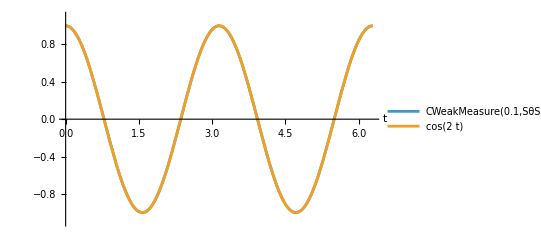

```mathematica
Plot[{CWeakMeasure[0.1,SθSpinHalf[Pi/2,#]&,t], Cos[2t]},{t,0,2 Pi },PlotRange->{-1.1,1.1}, PlotLegends->"Expressions", AxesLabel->{"t", None}]
```

Which is simply a cosine function. The Leggett-Garg function defined as  is

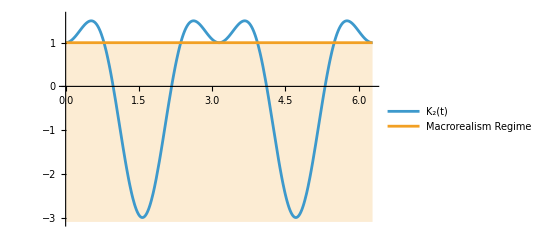

```mathematica
KWeakMeasure[β_,op_,t_]:=2CWeakMeasure[β,op,t]-CWeakMeasure[β,op,2t]
Plot[{KWeakMeasure[0.1,SθSpinHalf[Pi/2,#]&,t],1},{t,0,2Pi},PlotRange->{-3.1,1.6},Filling->{2->Bottom},PlotLegends->{"K_2(t)","Macrorealism Regime"}]
```

The Leggett-Garg  has been shown above to not obey the inequality  which indicates that the spin-1/2 system is properly quantum and does not evolve macro-realistically.

## Spin-1

The spin-1 system is the natural extension of the canonical spin-1/2 example to a three-level system, i.e. . However, as we will show, the three-level operator is already sufficiently different from the two-level operator that even for the simplest example of a spin-1 in a magnetic field, the traditional Leggett-Garg inequality is always satisfied. 

Leggett-Garg tests for n-level systems are typically dealt with in three ways:

1) Using the weak measure technique which provides a valid quantum correlation function for any n-level system.

2) The projector operator ΠSθnLevel can be easily fitted to be a 2-level operator with eigenvalues . This latter method is more popular in the literature and can be used to increase the value of  past the maximum allowed for a 2-level system .

3) We can use the same test with the traditionally defined  time correlation function, ignoring that  is a trichotomic/3-level operator. This works specifically because the expression  is still less than or equal to 1 for all values of . Even though the Leggett-Garg inequality is always satisfied for the spin-1 example, other three-level systems do exist which violate the Legget-Garg inequality. 

However, there is a fourth option which I have not seen explored in the literature which is to go back to the original LG bound and modify it for the additional possibility that  can now take the value of 0. For example,

As mentioned before, this inequality is still valid for three-level systems, however the right hand side is not equal to 1, as it was for 2-level operators. However, for all combinations of , the right hand side is only not equal to 1 when , in which case the right hand side is zero. Therefore,

.

Where the equality is point-wise for the three allowed values of  Substituting this in for the inequality and expanding the right hand side gives an inequality which is easily verifiable.

Plugging this into the Leggett-Garg inequality, multiplying each side by the probability , and then summing over the possibilities gives the updated Leggett-Garg inequality for three-level systems.

or

This last equation is our updated Leggett-Garg inequality for the three-level system. Note that I have rearranged the equation above it to preserve the structure . Now, let’s look at how this updated inequality plays out in the spin-1 example compared to the original LG inequality.

### Trichotomic LG bound

Our basis is now 3-dimensional corresponding to the three possible measurements of the spin of a spin-1 particle.

```mathematica
splus={1,0,0};
s0={0,1,0};
sminus={0,0,1};
StateVec = {splus, s0, sminus};
rho[H_,β_] := 1/Z[β] Sum[KroneckerProduct[S,S]*Exp[-β S.H.S],{S,StateVec}];
```

The spin operators of the spin-1 particle are now three-dimensional Hermitian matrices and are no longer unitary.

```mathematica
Sz = {{1,0,0},{0,0,0},{0,0,-1}};
Sx = 1/Sqrt[2]{{0,1,0},{1,0,1},{0,1,0}};
Sy =1/Sqrt[2]{{0,-I,0},{I,0,-I},{0,I,0}};
Id = IdentityMatrix[3];
Svec = {Sx,Sy,Sz};
```

As before, we will take the Hamiltonian to be of a magnetic field along the z-axis.

```mathematica
H =  -Sz;
H//MatrixForm
```

(-1 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

The projection operator for the three level system with eigenvalues {-1, 0, 1} is more involved than the two level system, but it is analytically solvable.

```mathematica
SθSpin1[θ_,t_]:=Udag[H,t].(Sin[θ]Sx +Cos[θ]Sz).U[H,t]
ΠSθ3Level[q_,t_]:=(1 - q^2)Id + 1/2(q SθSpin1[Pi/2,t]) + (3/2 q^2 - 1)SθSpin1[Pi/2,t].SθSpin1[Pi/2,t]
```

We will also initialize a function which implements the strong measure formula since the strong and weak measure formulas no longer coincide.

```mathematica
ThermalStateExpectation[H_,β_,op_]:=Tr[rho[H,β].op]
CqStrongMeasure[β_, op_,t_]:=Re[Sum[q1 q2 ThermalStateExpectation[H,β,op[q1,0].op[q2,t].op[q1,0]],{q1,{-1,0,1}},{q2,{-1,0,1}}]]
COneMinusQSquaredStrongMeasure[β_, op_,t_]:=Re[Sum[(1-q1^2)(1- q2^2) ThermalStateExpectation[H,β,op[q1,0].op[q2,t].op[q1,0]],{q1,{-1,0,1}},{q2,{-1,0,1}}]]
```

The strong measure formula can be used to calculate both  and .

LOW TEMPERATURE

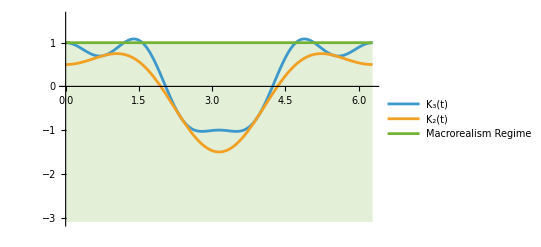

```mathematica
K3StrongMeasure[β_,op_,t_]:=2CqStrongMeasure[β,op,t]-CqStrongMeasure[β,op,2t]+COneMinusQSquaredStrongMeasure[β,op,2t]
K2StrongMeasure[β_,op_,t_]:=2CqStrongMeasure[β,op,t]-CqStrongMeasure[β,op,2t]
Plot[{K3StrongMeasure[100,ΠSθ3Level,t],K2StrongMeasure[100,ΠSθ3Level,t],1},{t,0,2Pi},PlotRange->{-3.1,1.6},Filling->{3->Bottom},PlotLegends->{"K_3(t)","K_2(t)","Macrorealism Regime"}]
```

HIGH TEMPERATURE

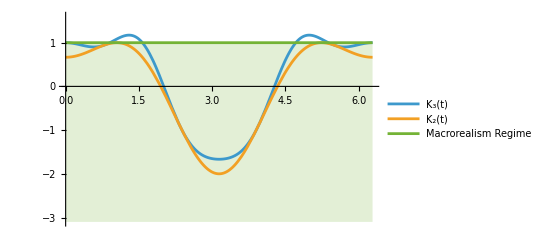

```mathematica
Plot[{K3StrongMeasure[.01,ΠSθ3Level,t],K2StrongMeasure[.01,ΠSθ3Level,t],1},{t,0,2Pi},PlotRange->{-3.1,1.6},Filling->{3->Bottom},PlotLegends->{"K_3(t)","K_2(t)","Macrorealism Regime"}]
```